```mathematica
Sort[Map[First,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]]]
```

{n123x4,n124x3,n12x34,n12x3x4,n12x3x4,n12x3x4,n134x2,n13x24,n13x2x4,n13x2x4,n13x2x4,n14x23,n14x2x3,n14x2x3,n14x2x3,n1x234,n1x23x4,n1x23x4,n1x23x4,n1x24x3,n1x24x3,n1x24x3,n1x2x34,n1x2x34,n1x2x34,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4}

```mathematica
StringCount [SymbolName[n1x2x34],"x"]
```

2

```mathematica
vertices=Sort[Sort[Map[First,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]]],StringCount [SymbolName[#1],"x"]>StringCount [SymbolName[#2],"x"]&]
```

{n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x34,n1x2x34,n1x2x34,n1x24x3,n1x24x3,n1x24x3,n1x23x4,n1x23x4,n1x23x4,n14x2x3,n14x2x3,n14x2x3,n13x2x4,n13x2x4,n13x2x4,n12x3x4,n12x3x4,n12x3x4,n1x234,n14x23,n13x24,n134x2,n12x34,n124x3,n123x4}

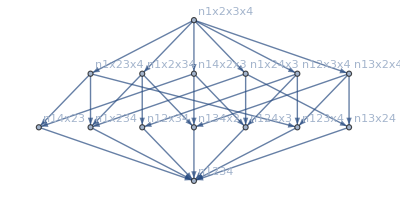

```mathematica
four=Graph[vertices,Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name"]
```

```mathematica
IM=IdentityMatrix[Length[VertexList[four]]];
```

```mathematica
fourM=AdjacencyMatrix[four];MatrixForm[fourM]
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MakeOne[mat_]:=Map[Map[If[#>0,1,0]&,#]&, mat]
```

```mathematica
ZetaM=MakeOne[Inverse[IM-fourM]];MatrixForm[ZetaM]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MobiusM=Inverse[ZetaM];MatrixForm[MobiusM,TableHeadings->{VertexList[four], VertexList[four]}]
```

( | n1x2x3x4 | n1x2x34 | n1x24x3 | n1x23x4 | n14x2x3 | n13x2x4 | n12x3x4 | n1x234 | n14x23 | n13x24 | n134x2 | n12x34 | n124x3 | n123x4 | n1234
n1x2x3x4 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | -6
n1x2x34 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 2
n1x24x3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 2
n1x23x4 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 2
n14x2x3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 2
n13x2x4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 2
n12x3x4 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 2
n1x234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
n14x23 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
n13x24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
n134x2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
n12x34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
n124x3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
n123x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
n1234 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Det[MobiusM]
```

1

```mathematica
MobiusM=Inverse[ZetaM];MatrixForm[MobiusM]
```

(1 | -1 | -1 | -1 | 2 | -1 | 1 | -1 | 1 | 2 | -1 | 1 | 2 | 2 | -6
0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 2
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

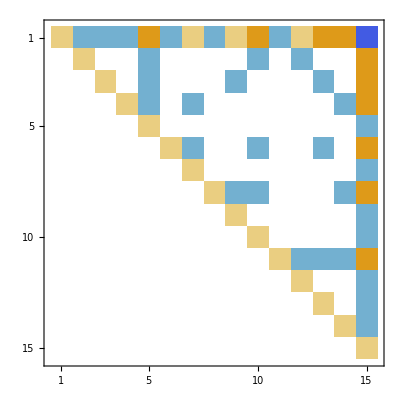

```mathematica
Inverse[ZetaM]//MatrixPlot
```

```mathematica
Subgraph
```

```mathematica
SumFrom[g_,v_]:=Block[{result=0},
Table[
result+=CalcMobius[g,
,{e,EdgeList[g,v->_]}
]
]
```

```mathematica
mob=Table[Null,{i,1,VertexCount[four]},{j,1,VertexCount[four]}]
```

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
CalcMobius[g_,low_,high_]:=Block[{temp},
If[ToString[low]==ToString[high],
1,
temp=-SumFrom[g,high];
temp
]
]
```

```mathematica
CalcMobius[four,n1234,n1234]
```

1

```mathematica
TopologicalSort[four]
```

{n1x2x3x4,n1x2x34,n1x24x3,n1x23x4,n1x234,n14x2x3,n14x23,n13x2x4,n13x24,n134x2,n12x3x4,n12x34,n124x3,n123x4,n1234}

```mathematica
GraphZeta[g_]:=Block[{ordered=TopologicalSort[four]},
Table[If[ToString[i]==ToString[j]||EdgeQ[g,i->j],1,0],{i,ordered},{j,ordered}]
]
```

```mathematica
GraphZeta[four]//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Inverse[GraphZeta[four]]//MatrixForm
```

(1 | -1 | -1 | -1 | 3 | -1 | 2 | -1 | 2 | 3 | -1 | 2 | 3 | 3 | -18
0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 3
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 3
0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 3
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)